```mathematica
Quit
```

```mathematica
LaunchKernels[36];
```

# Model of RDM-optimization

## Basic codes

### Hamiltonian matrix codes

#### generate matrix by alex (with μ and V)-new μ 1

```mathematica
Clear[manyBodyBasis,manyBodyHMatrix]

manyBodyBasis[{ℒ_,𝒩_},type_String]:=Module[{integerpartitions,range},
range=If[type=="Boson",Range[0,𝒩],{0,1}];
integerpartitions=IntegerPartitions[𝒩,{ℒ},range];(*列出整数N分成L个整数之和的所有排列可能,其中如果是费米子,每个组合的构成只能是0和1*)
ReverseSort@Flatten[Permutations/@integerpartitions,{{1,2},{3}}]
](*列出所有排列可能*)

manyBodyHMatrix[basis_,{t_,U_,V_,μ_,α_}]:=Module[{n=Length[basis],laticeNum=Length[basis[[1]]],hermitize=#+ #†&,diagonalU,diagonalV,diagonalμ,μbasis,Hoperatebasis1,positions1,rules1,Hoperatebasis2,positions2,rules2,T,T1,T2,interactionU,interactionV,potentialμ,μfactors,map,type,predicate},
type=If[Union[Flatten[basis]]=={0,1},"Fermion","Boson"];
map=If[n≤250,Map,ParallelMap];
diagonalU=Total[If[type=="Boson",#(#-1),SequenceCases[#,{p:1..}:>Length[{p}]-1]&~map~#]&[basis],{2}];(*1.玻色子只看#(#-1);2.(#-1)即basis每一项中的所有元素都-1;3.{2}表示对行求Total*)
diagonalV=Total[Table[MapThread[Times,{basis[[i]][[1;;laticeNum-1]],basis[[i]][[2;;laticeNum]]}],{i,Range[n]}],{2}];(*Subscript[n, i]*Subscript[n, i+1], when latticenum=3, there are 3 sites, we onlu need n1*n2+n2*n3, so here we set   basis[[i]][[1;;laticeNum-1]]*basis[[i]][[2;;laticeNum]] *)
μbasis=Table[basis[[i]][[j]] ⅇ^(I 2π α j),{i,n},{j,laticeNum}];
diagonalμ=Map[Total,μbasis];(*系数Cos[2π α j]根据J的值的求和*)
(*diagonalμ=Total[Table[basis[[i]],{i,Range[n]}],{2}];*)(*μ也是个对角阵，不过其的值之后basis的第一位有关，第一位为几，其系数就为几*)
predicate[n1_,n2_]:=If[type=="Boson",n1≥1,n1==1&&n2==0];
interactionU=U/2 SparseArray[{Band[{1,1}]->diagonalU},n(*n=Length[basis]*)](*1.band表示稀疏数组中以{i,j}开始的对角线带上的位置序列，这里指的是1，1开始对角线带上赋值diagonal的值；2.除了band之外，其余值均为0;3.n=Length[basis]阶的稀疏矩阵*);
interactionV=V  SparseArray[{Band[{1,1}]->diagonalV},n(*n=Length[basis]*)];
potentialμ=μ  SparseArray[{Band[{1,1}]->diagonalμ},n(*n=Length[basis]*)];
(*hopping part*)
(*最近邻跃迁*)Hoperatebasis1=ReplaceList[#,{a___,n1_,n2_,b___}:>({a,n1-1,n2+1,b}->√(n1(n2+1)))/;predicate[n1,n2]]&~map~basis;
positions1=Flatten[map[Position[basis,#,1]&,Keys[Hoperatebasis1],{2}],{{1},{2,3,4}}];
rules1=Flatten[Thread~map~Thread[MapIndexed[List[#,First[#2]]&,positions1,{2}]->Values[Hoperatebasis1]]];
(*周期性边界条件*)Hoperatebasis2=ReplaceList[#,{n1_,b___,n2_}:>({n1-1,b,n2+1}->√(n1(n2+1)))/;predicate[n1,n2]]&~map~basis;positions2=Flatten[map[Position[basis,#,1]&,Keys[Hoperatebasis2],{2}],{{1},{2,3,4}}];rules2=Flatten[Thread~map~Thread[MapIndexed[List[#,First[#2]]&,positions2,{2}]->Values[Hoperatebasis2]]];
T1=-t SparseArray[rules1,n];(*开放边界条件*)
T2=-t SparseArray[rules2,n];(*周期性边界条件*)
T=T1+T2;
hermitize[T]+interactionU+interactionV- potentialμ
]
```

#### get eigens

```mathematica
Clear[getEigenvalues,getEigenvectors,getEigensystem]
```

```mathematica
getEigenvalues[matrix_]:=Eigenvalues[matrix,Method->"Direct"]
```

```mathematica
getEigenvectors[matrix_]:=Eigenvectors[matrix,Method->"Direct"]
```

```mathematica
getEigensystem[matrix_]:=Eigensystem[matrix,Method->"Direct"]
```

### parameters (l=89,n=2)

```mathematica
latticenum=89;
particlenum=2;
```

```mathematica
Uvalues=Range[0,1,0.05];
Unum=Length[Uvalues];
```

```mathematica
μvalues=Range[0,1.5,0.05];(*select points*)
μnum=Length[μvalues];
```

```mathematica
matrixbasis=Block[{ℒ=latticenum,𝒩=particlenum},manyBodyBasis[{ℒ,𝒩},"Boson"]];
```

```mathematica
matrixbasis//Dimensions
matrixbasis//Length
```

{4005,89}

4005

```mathematica
eigennum=Length[matrixbasis]
```

4005

## FInished

## dynamic S_E U=0.8(t-0.01-3.02) Δt=0.01

### Basic

#### Import U=0.8,Ts

```mathematica
ψU08μTs=Import[NotebookDirectory[]<>"finalpsit_L89N2_U08_mus_t0.01.mx"];(*导入系统的本征态*)
```

```mathematica
ψU08μTs//Dimensions
```

{31,1001,4005}

```mathematica
(*ψ2=Import[NotebookDirectory[]<>"ED_vec_L89N2Tmu1_U08(0.6_1.1)_g(0_1.1_0.05)_hang_B.mx"];(*导入系统的本征态*)*)
```

```mathematica
RDMACoordinates=Import[NotebookDirectory[]<>"RDMACoordinates_L89N2_Sort_2.mx"];
```

```mathematica
RDMACoordinates//Dimensions
```

{1068255,2}

```mathematica
CordinateInDMAB=Import[NotebookDirectory[]<>"CordinateInDMAB_L89N2.mx"];
```

```mathematica
CordinateInDMAB//Dimensions
```

{1068255,2}

#### time --- Δt=0.01

```mathematica
Δt=0.01;
timenum=1;;303;
```

```mathematica
time=Range[1000];
```

```mathematica
U08P=First[Position[Uvalues,0.8]][[1]]
```

17

```mathematica
Export[NotebookDirectory[]<>"start_mark.txt",timenum];
```

### COMPUTE μ1

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=1;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

{303}

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

{303,982037}

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ2

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=2;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 3-4

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=3;;4;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 5-6

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=5;;6;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 7-8

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=7;;8;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 9-10

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=9;;10;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 11-12

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=11;;12;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 13-14

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=13;;14;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 15-16

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=15;;16;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 17-18

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=17;;18;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 19-20

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=19;;20;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 21-22

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=21;;22;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 23-24

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=23;;24;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 25-26

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=25;;26;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 27-28

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=27;;28;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 29-30

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=29;;30;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ31

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=31;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t0.01.mx"],RDMAmatrixU08μTs];
```

## EE U=0.8(t-0.01-3.02) Δt=0.01

### Import

#### ====1-10=================

```mathematica
RDMAmatrixU08μTs1=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu1_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs2=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu2_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs34=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu3;;4_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs56=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu5 ;; 6_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs78=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu7 ;; 8_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs910=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu9 ;; 10_Ts_L89N2_t0.01.mx"];
```

#### =========11-20===========

```mathematica
RDMAmatrixU08μTs1112=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu11 ;; 12_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs1314=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu13 ;; 14_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs1516=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu15 ;; 16_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs1718=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu17 ;; 18_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs1920=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu19 ;; 20_Ts_L89N2_t0.01.mx"];
```

#### =========21-31===========

```mathematica
RDMAmatrixU08μTs2122=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu21 ;; 22_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs2324=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu23 ;; 24_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs2526=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu25 ;; 26_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs2728=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu27 ;; 28_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs2930=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu29 ;; 30_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs31=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu31_Ts_L89N2_t0.01.mx"];
```

```mathematica
RDMAmatrixU08μTs=Join[RDMAmatrixU08μTs1,RDMAmatrixU08μTs2,2];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
timenum=%[[2]]
```

{3}

Part::partw: {3} 的部分 2 不存在.

{3}⟦2⟧

```mathematica
RDMAmatrixU08μTs//Dimensions
μnum=%[[1]]
```

{3}

3

### Join

#### μ 1-10

```mathematica
RDMAmatrixU08μTs12=Join[{RDMAmatrixU08μTs1},{RDMAmatrixU08μTs2}];
```

```mathematica
RDMAmatrixU08μTs12//Dimensions
```

{2,303,1035,1035}

```mathematica
RDMAmatrixU08μTs310=Join[RDMAmatrixU08μTs34,RDMAmatrixU08μTs56,RDMAmatrixU08μTs78,RDMAmatrixU08μTs910];
%//Dimensions
```

{8,303,1035,1035}

```mathematica
RDMAmatrixU08μTs110=Join[RDMAmatrixU08μTs12,RDMAmatrixU08μTs310];
%//Dimensions
```

{10,303,1035,1035}

#### μ 11-20

```mathematica
RDMAmatrixU08μTs1120=Join[RDMAmatrixU08μTs1112,RDMAmatrixU08μTs1314,RDMAmatrixU08μTs1516,RDMAmatrixU08μTs1718,RDMAmatrixU08μTs1920];
```

```mathematica
RDMAmatrixU08μTs1120//Dimensions
```

{10,303,1035,1035}

#### μ 21-31

```mathematica
RDMAmatrixU08μTs2131=Join[RDMAmatrixU08μTs2122,RDMAmatrixU08μTs2324,RDMAmatrixU08μTs2526,RDMAmatrixU08μTs2728,RDMAmatrixU08μTs2930,{RDMAmatrixU08μTs31}];
```

```mathematica
RDMAmatrixU08μTs2131//Dimensions
```

{11,303,1035,1035}

### EE-U08μTs Δt-1-10 head

```mathematica
RDMAmatrixU08μTs=RDMAmatrixU08μTs110;
```

```mathematica
μnum=Dimensions[RDMAmatrixU08μTs][[1]]
timenum=Dimensions[RDMAmatrixU08μTs][[2]]
```

10

303

#### Ω_A^N_A(Ω_A^1,Ω_A^2,Ω_A^3)-BlockdigElementsU08μTs

```mathematica
timenum
```

303

```mathematica
μnum
```

10

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{10,303,1035,1035}

```mathematica
BlockdigElementsU08μTs=Table[BlockDiagonalMatrix[RDMAmatrixU08μTs[[μp]][[timeP]]]["Blocks"],{μp,μnum},{timeP,2,timenum}];
```

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
(*timenum=timenum-1*)
```

302

```mathematica
(*Export[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t0.01.mx",BlockdigElementsU08μTs];*)
```

```mathematica
(*BlockdigElementsU08μTs=Import[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t0.01.mx"];*)
```

三个block矩阵的维度

```mathematica
(*ΩA1dim=Length[BlockdigElementsU08μTs[[1]][[1]][[1]]]
ΩA2dim=Length[BlockdigElementsU08μTs[[1]][[1]][[2]]]
ΩA3dim=Length[BlockdigElementsU08μTs[[1]][[1]][[3]]]*)
```

#### λ_α^N_a - RDMeigensU08μTs

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

{31,301,3}

```mathematica
RDMeigensU08μTs=Map[Eigenvalues,BlockdigElementsU08μTs,{3}];
```

```mathematica
(*RDMeigensU08μTs//Dimensions*)
```

{31,301,3}

```mathematica
Export[NotebookDirectory[]<>"RDMeigensU08μTs_L89N2_mu1;;10_Sort_2_t0.01.mx",RDMeigensU08μTs];
```

#### P_N_A - PNAU08μTs

```mathematica
Total/@(RDMeigensU08μTs[[-1]][[-1]])
```

{0.282861,0.509696,0.207443}

```mathematica
PNAU08μTs=Map[Total,RDMeigensU08μTs,{3}];
```

```mathematica
PNAU08μTs//Dimensions
```

{10,302,3}

#### (λ̃)_α^N_a - subRDMeigensU08μTs

```mathematica
subRDMeigensU08μTs=RDMeigensU08μTs/PNAU08μTs;
```

```mathematica
subRDMeigensU08μTs//Dimensions
```

{10,302,3}

#### S_num

```mathematica
SnumU08μTs=-Map[Total,PNAU08μTs*Log[PNAU08μTs],{2}];
```

```mathematica
SnumU08μTs//Dimensions
```

{10,302}

```mathematica
Export[NotebookDirectory[]<>"SnumU08μTs_L89N2_mu1;;10_Sort_2_t0.01.mx",SnumU08μTs];
```

```mathematica
MinMax[SnumU08μTs[[1]]]
```

{0.00190331,1.06215}

```mathematica
{0.001903312475601993,1.08627}
```

{0.00190331,1.08627}

```mathematica
(*Map[Position[SnumU08μTs,#]&,MinMax[SnumU08μTs]]*)
```

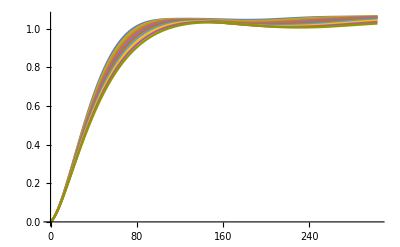

```mathematica
ListLinePlot[SnumU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_conf

```mathematica
PNAU08μTs//Dimensions
subRDMeigensU08μTs//Dimensions
```

{10,302,3}

{10,302,3}

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
SconfNsU08μTs=-Map[Total,(PNAU08μTs*subRDMeigensU08μTs*Log[subRDMeigensU08μTs]),{3}];
```

```mathematica
SconfNsU08μTs//Dimensions
```

{10,302,3}

```mathematica
SconfN1U08μTs=SconfNsU08μTs[[All,All,1]];
SconfN2U08μTs=SconfNsU08μTs[[All,All,2]];
SconfN3U08μTs=SconfNsU08μTs[[All,All,3]];
```

```mathematica
SconfN1U08μTs//Dimensions
SconfN2U08μTs//Dimensions
SconfN3U08μTs//Dimensions
```

{10,302}

{10,302}

{10,302}

```mathematica
SconfU08μTs=Plus[SconfN1U08μTs,SconfN2U08μTs,SconfN3U08μTs];
%//Dimensions
```

{10,302}

```mathematica
Export[NotebookDirectory[]<>"SconfU08μTs_L89N2_mu1;;10_Sort_2_t0.01.mx",SconfU08μTs];
```

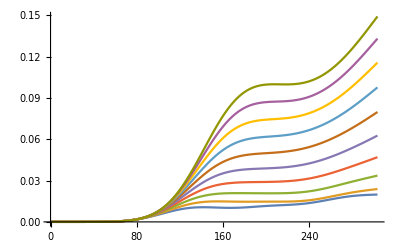

```mathematica
ListLinePlot[SconfU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_tot

```mathematica
StotU08μTs=SnumU08μTs+SconfU08μTs;
%//Dimensions
```

{10,302}

```mathematica
Export[NotebookDirectory[]<>"StotU08μTs_L89N2_mu1;;10_Sort_2_t0.01.mx",StotU08μTs];
```

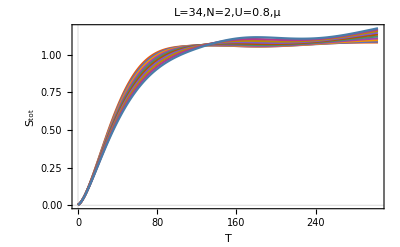

```mathematica
ListLinePlot[StotU08μTs,DataRange->MinMax@{0,timenum},PlotTheme->{"LargeLabels","SansLabels","Scientific"},FrameLabel->{"T","S_tot"},PlotLabel->"L=89,N=2,U=0.8,μ",PlotRange->All]
```

### EE-U08μTs Δt-11-20 head

```mathematica
RDMAmatrixU08μTs=RDMAmatrixU08μTs1120;
```

```mathematica
μnum=Dimensions[RDMAmatrixU08μTs][[1]]
timenum=Dimensions[RDMAmatrixU08μTs][[2]]
```

10

303

#### Ω_A^N_A(Ω_A^1,Ω_A^2,Ω_A^3)-BlockdigElementsU08μTs

```mathematica
timenum
```

303

```mathematica
μnum
```

10

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{10,303,1035,1035}

```mathematica
BlockdigElementsU08μTs=Table[BlockDiagonalMatrix[RDMAmatrixU08μTs[[μp]][[timeP]]]["Blocks"],{μp,μnum},{timeP,2,timenum}];
```

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
(*timenum=timenum-1*)
```

```mathematica
(*Export[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t0.01.mx",BlockdigElementsU08μTs];*)
```

```mathematica
(*BlockdigElementsU08μTs=Import[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t0.01.mx"];*)
```

三个block矩阵的维度

```mathematica
(*ΩA1dim=Length[BlockdigElementsU08μTs[[1]][[1]][[1]]]
ΩA2dim=Length[BlockdigElementsU08μTs[[1]][[1]][[2]]]
ΩA3dim=Length[BlockdigElementsU08μTs[[1]][[1]][[3]]]*)
```

#### λ_α^N_a - RDMeigensU08μTs

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
RDMeigensU08μTs=Map[Eigenvalues,BlockdigElementsU08μTs,{3}];
```

```mathematica
(*RDMeigensU08μTs//Dimensions*)
```

```mathematica
Export[NotebookDirectory[]<>"RDMeigensU08μTs_L89N2_mu11;;20_Sort_2_t0.01.mx",RDMeigensU08μTs];
```

#### P_N_A - PNAU08μTs

```mathematica
Total/@(RDMeigensU08μTs[[-1]][[-1]])
```

{0.383299,0.501638,0.115062}

```mathematica
PNAU08μTs=Map[Total,RDMeigensU08μTs,{3}];
```

```mathematica
PNAU08μTs//Dimensions
```

{10,302,3}

#### (λ̃)_α^N_a - subRDMeigensU08μTs

```mathematica
subRDMeigensU08μTs=RDMeigensU08μTs/PNAU08μTs;
```

```mathematica
subRDMeigensU08μTs//Dimensions
```

{10,302,3}

#### S_num

```mathematica
SnumU08μTs=-Map[Total,PNAU08μTs*Log[PNAU08μTs],{2}];
```

```mathematica
SnumU08μTs//Dimensions
```

{10,302}

```mathematica
Export[NotebookDirectory[]<>"SnumU08μTs_L89N2_mu11;;20_Sort_2_t0.01.mx",SnumU08μTs];
```

```mathematica
MinMax[SnumU08μTs[[1]]]
```

{0.00188751,1.03088}

```mathematica
{0.001903312475601993,1.08627}
```

{0.00190331,1.08627}

```mathematica
(*Map[Position[SnumU08μTs,#]&,MinMax[SnumU08μTs]]*)
```

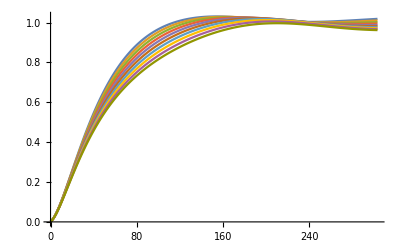

```mathematica
ListLinePlot[SnumU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_conf

```mathematica
PNAU08μTs//Dimensions
subRDMeigensU08μTs//Dimensions
```

{10,302,3}

{10,302,3}

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
SconfNsU08μTs=-Map[Total,(PNAU08μTs*subRDMeigensU08μTs*Log[subRDMeigensU08μTs]),{3}];
```

```mathematica
SconfNsU08μTs//Dimensions
```

{10,302,3}

```mathematica
SconfN1U08μTs=SconfNsU08μTs[[All,All,1]];
SconfN2U08μTs=SconfNsU08μTs[[All,All,2]];
SconfN3U08μTs=SconfNsU08μTs[[All,All,3]];
```

```mathematica
SconfN1U08μTs//Dimensions
SconfN2U08μTs//Dimensions
SconfN3U08μTs//Dimensions
```

{10,302}

{10,302}

{10,302}

```mathematica
SconfU08μTs=Plus[SconfN1U08μTs,SconfN2U08μTs,SconfN3U08μTs];
%//Dimensions
```

{10,302}

```mathematica
Export[NotebookDirectory[]<>"SconfU08μTs_L89N2_mu11;;20_Sort_2_t0.01.mx",SconfU08μTs];
```

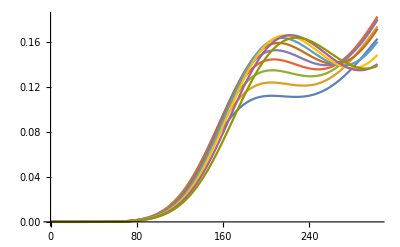

```mathematica
ListLinePlot[SconfU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_tot

```mathematica
StotU08μTs=SnumU08μTs+SconfU08μTs;
%//Dimensions
```

{10,302}

```mathematica
Export[NotebookDirectory[]<>"StotU08μTs_L89N2_mu11;;20_Sort_2_t0.01.mx",StotU08μTs];
```

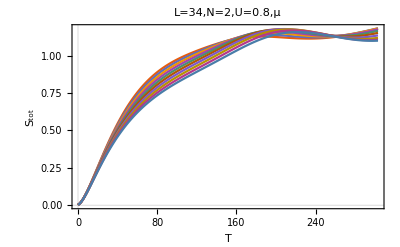

```mathematica
ListLinePlot[StotU08μTs,DataRange->MinMax@{0,timenum},PlotTheme->{"LargeLabels","SansLabels","Scientific"},FrameLabel->{"T","S_tot"},PlotLabel->"L=89,N=2,U=0.8,μ",PlotRange->All]
```

### EE-U08μTs Δt-21-31 head

```mathematica
RDMAmatrixU08μTs=RDMAmatrixU08μTs2131;
```

```mathematica
μnum=Dimensions[RDMAmatrixU08μTs][[1]]
timenum=Dimensions[RDMAmatrixU08μTs][[2]]
```

11

303

#### Ω_A^N_A(Ω_A^1,Ω_A^2,Ω_A^3)-BlockdigElementsU08μTs

```mathematica
timenum
```

303

```mathematica
μnum
```

11

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{11,303,1035,1035}

```mathematica
BlockdigElementsU08μTs=Table[BlockDiagonalMatrix[RDMAmatrixU08μTs[[μp]][[timeP]]]["Blocks"],{μp,μnum},{timeP,2,timenum}];
```

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
(*timenum=timenum-1*)
```

```mathematica
(*Export[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t0.01.mx",BlockdigElementsU08μTs];*)
```

```mathematica
(*BlockdigElementsU08μTs=Import[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t0.01.mx"];*)
```

三个block矩阵的维度

```mathematica
(*ΩA1dim=Length[BlockdigElementsU08μTs[[1]][[1]][[1]]]
ΩA2dim=Length[BlockdigElementsU08μTs[[1]][[1]][[2]]]
ΩA3dim=Length[BlockdigElementsU08μTs[[1]][[1]][[3]]]*)
```

#### λ_α^N_a - RDMeigensU08μTs

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
RDMeigensU08μTs=Map[Eigenvalues,BlockdigElementsU08μTs,{3}];
```

```mathematica
(*RDMeigensU08μTs//Dimensions*)
```

```mathematica
Export[NotebookDirectory[]<>"RDMeigensU08μTs_L89N2_mu21;;31_Sort_2_t0.01.mx",RDMeigensU08μTs];
```

#### P_N_A - PNAU08μTs

```mathematica
Total/@(RDMeigensU08μTs[[-1]][[-1]])
```

{0.716675,0.255737,0.0275885}

```mathematica
PNAU08μTs=Map[Total,RDMeigensU08μTs,{3}];
```

```mathematica
PNAU08μTs//Dimensions
```

{11,302,3}

#### (λ̃)_α^N_a - subRDMeigensU08μTs

```mathematica
subRDMeigensU08μTs=RDMeigensU08μTs/PNAU08μTs;
```

```mathematica
subRDMeigensU08μTs//Dimensions
```

{11,302,3}

#### S_num

```mathematica
SnumU08μTs=-Map[Total,PNAU08μTs*Log[PNAU08μTs],{2}];
```

```mathematica
SnumU08μTs//Dimensions
```

{11,302}

```mathematica
Export[NotebookDirectory[]<>"SnumU08μTs_L89N2_mu21;;31_Sort_2_t0.01.mx",SnumU08μTs];
```

```mathematica
MinMax[SnumU08μTs[[1]]]
```

{0.00187187,0.985968}

```mathematica
{0.001903312475601993,1.08627}
```

{0.00190331,1.08627}

```mathematica
(*Map[Position[SnumU08μTs,#]&,MinMax[SnumU08μTs]]*)
```

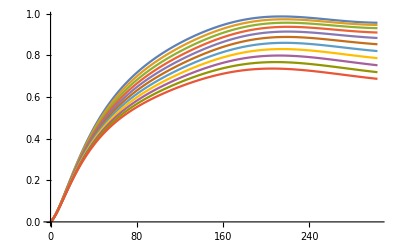

```mathematica
ListLinePlot[SnumU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_conf

```mathematica
PNAU08μTs//Dimensions
subRDMeigensU08μTs//Dimensions
```

{11,302,3}

{11,302,3}

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
SconfNsU08μTs=-Map[Total,(PNAU08μTs*subRDMeigensU08μTs*Log[subRDMeigensU08μTs]),{3}];
```

```mathematica
SconfNsU08μTs//Dimensions
```

{11,302,3}

```mathematica
SconfN1U08μTs=SconfNsU08μTs[[All,All,1]];
SconfN2U08μTs=SconfNsU08μTs[[All,All,2]];
SconfN3U08μTs=SconfNsU08μTs[[All,All,3]];
```

```mathematica
SconfN1U08μTs//Dimensions
SconfN2U08μTs//Dimensions
SconfN3U08μTs//Dimensions
```

{11,302}

{11,302}

{11,302}

```mathematica
SconfU08μTs=Plus[SconfN1U08μTs,SconfN2U08μTs,SconfN3U08μTs];
%//Dimensions
```

{11,302}

```mathematica
Export[NotebookDirectory[]<>"SconfU08μTs_L89N2_mu21;;31_Sort_2_t0.01.mx",SconfU08μTs];
```

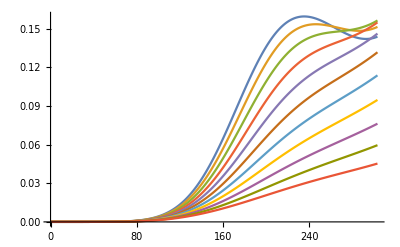

```mathematica
ListLinePlot[SconfU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_tot

```mathematica
StotU08μTs=SnumU08μTs+SconfU08μTs;
%//Dimensions
```

{11,302}

```mathematica
Export[NotebookDirectory[]<>"StotU08μTs_L89N2_mu21;;31_Sort_2_t0.01.mx",StotU08μTs];
```

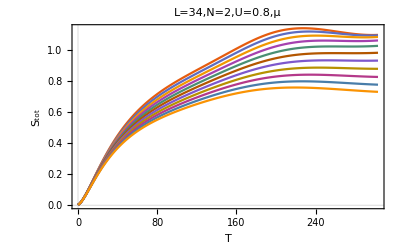

```mathematica
ListLinePlot[StotU08μTs,DataRange->MinMax@{0,timenum},PlotTheme->{"LargeLabels","SansLabels","Scientific"},FrameLabel->{"T","S_tot"},PlotLabel->"L=89,N=2,U=0.8,μ",PlotRange->All]
```

## dynamic S_E U=0.8(t-1-300) Δt=1. (ING)

### Basic

#### Import U=0.8,Ts

```mathematica
ψU08μTs=Import[NotebookDirectory[]<>"finalpsit_L89N2_U08_mus_t1.mx"];(*导入系统的本征态*)
```

```mathematica
ψU08μTs//Dimensions
```

{31,1001,4005}

```mathematica
(*ψ2=Import[NotebookDirectory[]<>"ED_vec_L89N2Tmu1_U08(0.6_1.1)_g(0_1.1_0.05)_hang_B.mx"];(*导入系统的本征态*)*)
```

```mathematica
RDMACoordinates=Import[NotebookDirectory[]<>"RDMACoordinates_L89N2_Sort_2.mx"];
```

```mathematica
RDMACoordinates//Dimensions
```

{1068255,2}

```mathematica
CordinateInDMAB=Import[NotebookDirectory[]<>"CordinateInDMAB_L89N2.mx"];
```

```mathematica
CordinateInDMAB//Dimensions
```

{1068255,2}

#### time --- Δt=1

```mathematica
Δt=1;
timenum=1;;300;
```

```mathematica
time=Range[1000];
```

```mathematica
U08P=First[Position[Uvalues,0.8]][[1]]
```

17

```mathematica
Export[NotebookDirectory[]<>"start_mark.txt",timenum];
```

### 1.COMPUTE μ 1-2

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=1;;2;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 2.COMPUTE μ 3-4

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=3;;4;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 3.COMPUTE μ 5-6

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=5;;6;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 4.COMPUTE μ 7-8

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=7;;8;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 5.COMPUTE μ 9-10

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=9;;10;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 6.COMPUTE μ 11-12

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=11;;12;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 7.COMPUTE μ 13-14

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=13;;14;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 8.COMPUTE μ 15-16

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=15;;16;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 9.COMPUTE μ 17-18

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=17;;18;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 10.COMPUTE μ 19-20

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=19;;20;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 11.COMPUTE μ 21-22

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=21;;22;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 12.COMPUTE μ 23-24

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=23;;24;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 13.COMPUTE μ 25-26

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=25;;26;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 14.COMPUTE μ 27-28

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=27;;28;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 15.COMPUTE μ 29-30

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=29;;30;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### 16.COMPUTE μ31

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=31;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{300,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,300,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{300,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{300,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{300,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{300,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

## ING

## EE U=0.8(t-1-300) Δt=1

### Import

#### ====1-10=================

```mathematica
RDMAmatrixU08μTs12=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0., 0.05}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs34=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.1, 0.15}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs56=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.2, 0.25}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs78=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.3, 0.35}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs910=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.4, 0.45}_Ts_L89N2_t{1, 300}_t1.mx"];
```

#### =========11-20===========

```mathematica
RDMAmatrixU08μTs1112=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.5, 0.55}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs1314=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.6, 0.65}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs1516=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.7, 0.75}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs1718=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.8, 0.85}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs1920=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{0.9, 0.95}_Ts_L89N2_t{1, 300}_t1.mx"];
```

#### =========21-31===========

```mathematica
RDMAmatrixU08μTs2122=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{1., 1.05}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs2324=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{1.1, 1.15}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs2526=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{1.2, 1.25}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs2728=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{1.3, 1.35}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs2930=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{1.4, 1.45}_Ts_L89N2_t{1, 300}_t1.mx"];
```

```mathematica
RDMAmatrixU08μTs31=Import[NotebookDirectory[]<>"RDMAmatrix_U08_mu{1.5, 1.5}_Ts_L89N2_t{1, 300}_t1.mx"];
```

### Join

#### μ 1-10

```mathematica
RDMAmatrixU08μTs110=Join[RDMAmatrixU08μTs12,RDMAmatrixU08μTs34,RDMAmatrixU08μTs56,RDMAmatrixU08μTs78,RDMAmatrixU08μTs910];
%//Dimensions
```

{10,300,1035,1035}

#### μ 11-20

```mathematica
RDMAmatrixU08μTs1120=Join[RDMAmatrixU08μTs1112,RDMAmatrixU08μTs1314,RDMAmatrixU08μTs1516,RDMAmatrixU08μTs1718,RDMAmatrixU08μTs1920];
```

```mathematica
RDMAmatrixU08μTs1120//Dimensions
```

{10,300,1035,1035}

#### μ 21-31

```mathematica
RDMAmatrixU08μTs2131=Join[RDMAmatrixU08μTs2122,RDMAmatrixU08μTs2324,RDMAmatrixU08μTs2526,RDMAmatrixU08μTs2728,RDMAmatrixU08μTs2930,{RDMAmatrixU08μTs31}];
```

```mathematica
RDMAmatrixU08μTs2131//Dimensions
```

{11,300,1035,1035}

### EE-U08μTs Δt-1-10 head

```mathematica
RDMAmatrixU08μTs=RDMAmatrixU08μTs110;
```

```mathematica
μnum=Dimensions[RDMAmatrixU08μTs][[1]]
timenum=Dimensions[RDMAmatrixU08μTs][[2]]
```

10

300

#### Ω_A^N_A(Ω_A^1,Ω_A^2,Ω_A^3)-BlockdigElementsU08μTs

```mathematica
timenum
```

300

```mathematica
μnum
```

10

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{10,300,1035,1035}

```mathematica
BlockdigElementsU08μTs=Table[BlockDiagonalMatrix[RDMAmatrixU08μTs[[μp]][[timeP]]]["Blocks"],{μp,μnum},{timeP,2,timenum}];
```

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
(*timenum=timenum-1*)
```

```mathematica
(*Export[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2.mx",BlockdigElementsU08μTs];*)
```

```mathematica
(*BlockdigElementsU08μTs=Import[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2.mx"];*)
```

三个block矩阵的维度

```mathematica
(*ΩA1dim=Length[BlockdigElementsU08μTs[[1]][[1]][[1]]]
ΩA2dim=Length[BlockdigElementsU08μTs[[1]][[1]][[2]]]
ΩA3dim=Length[BlockdigElementsU08μTs[[1]][[1]][[3]]]*)
```

#### λ_α^N_a - RDMeigensU08μTs

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
RDMeigensU08μTs=Map[Eigenvalues,BlockdigElementsU08μTs,{3}];
```

```mathematica
(*RDMeigensU08μTs//Dimensions*)
```

```mathematica
Export[NotebookDirectory[]<>"RDMeigensU08μTs_L89N2_mu1;;10_Sort_2_t1.mx",RDMeigensU08μTs];
```

#### P_N_A - PNAU08μTs

```mathematica
Total/@(RDMeigensU08μTs[[-1]][[-1]])
```

{0.256107,0.489568,0.254325}

```mathematica
PNAU08μTs=Map[Total,RDMeigensU08μTs,{3}];
```

```mathematica
PNAU08μTs//Dimensions
```

{10,299,3}

#### (λ̃)_α^N_a - subRDMeigensU08μTs

```mathematica
subRDMeigensU08μTs=RDMeigensU08μTs/PNAU08μTs;
```

```mathematica
subRDMeigensU08μTs//Dimensions
```

{10,299,3}

#### S_num

```mathematica
SnumU08μTs=-Map[Total,PNAU08μTs*Log[PNAU08μTs],{2}];
```

```mathematica
SnumU08μTs//Dimensions
```

{10,299}

```mathematica
Export[NotebookDirectory[]<>"SnumU08μTs_L89N2_mu1;;10_Sort_2_t1.mx",SnumU08μTs];
```

```mathematica
MinMax[SnumU08μTs[[1]]]
```

{1.04605,1.09859}

```mathematica
{0.001903312475601993,1.08627}
```

{0.00190331,1.08627}

```mathematica
(*Map[Position[SnumU08μTs,#]&,MinMax[SnumU08μTs]]*)
```

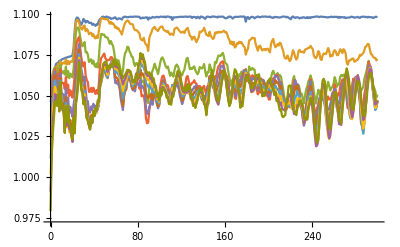

```mathematica
ListLinePlot[SnumU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_conf

```mathematica
PNAU08μTs//Dimensions
subRDMeigensU08μTs//Dimensions
```

{10,299,3}

{10,299,3}

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
SconfNsU08μTs=-Map[Total,(PNAU08μTs*subRDMeigensU08μTs*Log[subRDMeigensU08μTs]),{3}];
```

```mathematica
SconfNsU08μTs//Dimensions
```

{10,299,3}

```mathematica
SconfN1U08μTs=SconfNsU08μTs[[All,All,1]];
SconfN2U08μTs=SconfNsU08μTs[[All,All,2]];
SconfN3U08μTs=SconfNsU08μTs[[All,All,3]];
```

```mathematica
SconfN1U08μTs//Dimensions
SconfN2U08μTs//Dimensions
SconfN3U08μTs//Dimensions
```

{10,299}

{10,299}

{10,299}

```mathematica
SconfU08μTs=Plus[SconfN1U08μTs,SconfN2U08μTs,SconfN3U08μTs];
%//Dimensions
```

{10,299}

```mathematica
Export[NotebookDirectory[]<>"SconfU08μTs_L89N2_mu1;;10_Sort_2_t1.mx",SconfU08μTs];
```

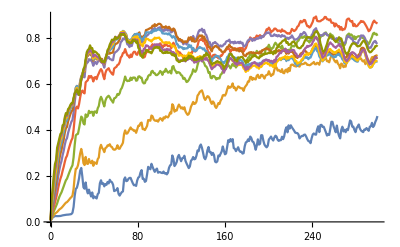

```mathematica
ListLinePlot[SconfU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_tot

```mathematica
StotU08μTs=SnumU08μTs+SconfU08μTs;
%//Dimensions
```

{10,299}

```mathematica
Export[NotebookDirectory[]<>"StotU08μTs_L89N2_mu1;;10_Sort_2_t1.mx",StotU08μTs];
```

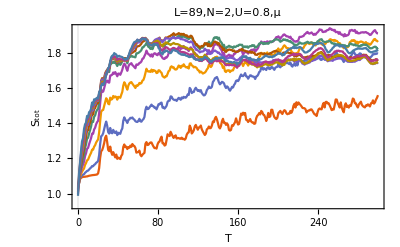

```mathematica
ListLinePlot[StotU08μTs,DataRange->MinMax@{0,timenum},PlotTheme->{"LargeLabels","SansLabels","Scientific"},FrameLabel->{"T","S_tot"},PlotLabel->"L=89,N=2,U=0.8,μ",PlotRange->All]
```

### EE-U08μTs Δt-11-20 head

```mathematica
RDMAmatrixU08μTs=RDMAmatrixU08μTs1120;
```

```mathematica
μnum=Dimensions[RDMAmatrixU08μTs][[1]]
timenum=Dimensions[RDMAmatrixU08μTs][[2]]
```

10

300

#### Ω_A^N_A(Ω_A^1,Ω_A^2,Ω_A^3)-BlockdigElementsU08μTs

```mathematica
timenum
```

300

```mathematica
μnum
```

10

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{10,300,1035,1035}

```mathematica
BlockdigElementsU08μTs=Table[BlockDiagonalMatrix[RDMAmatrixU08μTs[[μp]][[timeP]]]["Blocks"],{μp,μnum},{timeP,2,timenum}];
```

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
(*timenum=timenum-1*)
```

```mathematica
(*Export[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t1.mx",BlockdigElementsU08μTs];*)
```

```mathematica
(*BlockdigElementsU08μTs=Import[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t1.mx"];*)
```

三个block矩阵的维度

```mathematica
(*ΩA1dim=Length[BlockdigElementsU08μTs[[1]][[1]][[1]]]
ΩA2dim=Length[BlockdigElementsU08μTs[[1]][[1]][[2]]]
ΩA3dim=Length[BlockdigElementsU08μTs[[1]][[1]][[3]]]*)
```

#### λ_α^N_a - RDMeigensU08μTs

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
RDMeigensU08μTs=Map[Eigenvalues,BlockdigElementsU08μTs,{3}];
```

```mathematica
(*RDMeigensU08μTs//Dimensions*)
```

```mathematica
Export[NotebookDirectory[]<>"RDMeigensU08μTs_L89N2_mu11;;20_Sort_2_t1.mx",RDMeigensU08μTs];
```

#### P_N_A - PNAU08μTs

```mathematica
Total/@(RDMeigensU08μTs[[-1]][[-1]])
```

{0.905734,0.0888491,0.00541661}

```mathematica
PNAU08μTs=Map[Total,RDMeigensU08μTs,{3}];
```

```mathematica
PNAU08μTs//Dimensions
```

{10,299,3}

#### (λ̃)_α^N_a - subRDMeigensU08μTs

```mathematica
subRDMeigensU08μTs=RDMeigensU08μTs/PNAU08μTs;
```

```mathematica
subRDMeigensU08μTs//Dimensions
```

{10,299,3}

#### S_num

```mathematica
SnumU08μTs=-Map[Total,PNAU08μTs*Log[PNAU08μTs],{2}];
```

```mathematica
SnumU08μTs//Dimensions
```

{10,299}

```mathematica
Export[NotebookDirectory[]<>"SnumU08μTs_L89N2_mu11;;20_Sort_2.mx",SnumU08μTs];
```

```mathematica
MinMax[SnumU08μTs[[1]]]
```

{0.966191,1.07653}

```mathematica
{0.001903312475601993,1.08627}
```

{0.00190331,1.08627}

```mathematica
(*Map[Position[SnumU08μTs,#]&,MinMax[SnumU08μTs]]*)
```

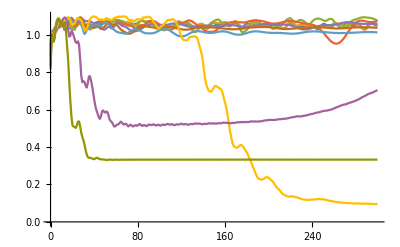

```mathematica
ListLinePlot[SnumU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_conf

```mathematica
PNAU08μTs//Dimensions
subRDMeigensU08μTs//Dimensions
```

{10,299,3}

{10,299,3}

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
SconfNsU08μTs=-Map[Total,(PNAU08μTs*subRDMeigensU08μTs*Log[subRDMeigensU08μTs]),{3}];
```

```mathematica
SconfNsU08μTs//Dimensions
```

{10,299,3}

```mathematica
SconfN1U08μTs=SconfNsU08μTs[[All,All,1]];
SconfN2U08μTs=SconfNsU08μTs[[All,All,2]];
SconfN3U08μTs=SconfNsU08μTs[[All,All,3]];
```

```mathematica
SconfN1U08μTs//Dimensions
SconfN2U08μTs//Dimensions
SconfN3U08μTs//Dimensions
```

{10,299}

{10,299}

{10,299}

```mathematica
SconfU08μTs=Plus[SconfN1U08μTs,SconfN2U08μTs,SconfN3U08μTs];
%//Dimensions
```

{10,299}

```mathematica
Export[NotebookDirectory[]<>"SconfU08μTs_L89N2_mu11;;20_Sort_2_t1.mx",SconfU08μTs];
```

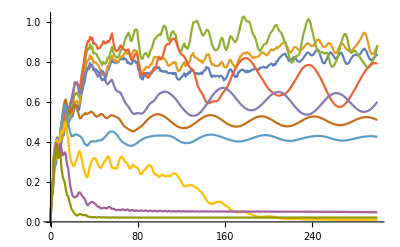

```mathematica
ListLinePlot[SconfU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_tot

```mathematica
StotU08μTs=SnumU08μTs+SconfU08μTs;
%//Dimensions
```

{10,299}

```mathematica
Export[NotebookDirectory[]<>"StotU08μTs_L89N2_mu11;;20_Sort_2_t1.mx",StotU08μTs];
```

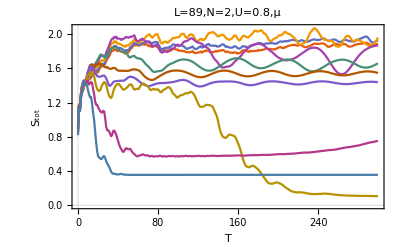

```mathematica
ListLinePlot[StotU08μTs,DataRange->MinMax@{0,timenum},PlotTheme->{"LargeLabels","SansLabels","Scientific"},FrameLabel->{"T","S_tot"},PlotLabel->"L=89,N=2,U=0.8,μ",PlotRange->All]
```

### EE-U08μTs Δt-21-31 head

```mathematica
RDMAmatrixU08μTs=RDMAmatrixU08μTs2131;
```

```mathematica
μnum=Dimensions[RDMAmatrixU08μTs][[1]]
timenum=Dimensions[RDMAmatrixU08μTs][[2]]
```

11

300

#### Ω_A^N_A(Ω_A^1,Ω_A^2,Ω_A^3)-BlockdigElementsU08μTs

```mathematica
timenum
```

300

```mathematica
μnum
```

11

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{11,300,1035,1035}

```mathematica
BlockdigElementsU08μTs=Table[BlockDiagonalMatrix[RDMAmatrixU08μTs[[μp]][[timeP]]]["Blocks"],{μp,μnum},{timeP,2,timenum}];
```

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
(*timenum=timenum-1*)
```

```mathematica
(*Export[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t1.mx",BlockdigElementsU08μTs];*)
```

```mathematica
(*BlockdigElementsU08μTs=Import[NotebookDirectory[]<>"BlockdigElementsU08μTs_L89N2_Sort_2_t1.mx"];*)
```

三个block矩阵的维度

```mathematica
(*ΩA1dim=Length[BlockdigElementsU08μTs[[1]][[1]][[1]]]
ΩA2dim=Length[BlockdigElementsU08μTs[[1]][[1]][[2]]]
ΩA3dim=Length[BlockdigElementsU08μTs[[1]][[1]][[3]]]*)
```

#### λ_α^N_a - RDMeigensU08μTs

```mathematica
(*BlockdigElementsU08μTs//Dimensions*)
```

```mathematica
RDMeigensU08μTs=Map[Eigenvalues,BlockdigElementsU08μTs,{3}];
```

```mathematica
(*RDMeigensU08μTs//Dimensions*)
```

```mathematica
Export[NotebookDirectory[]<>"RDMeigensU08μTs_L89N2_mu21;;31_Sort_2_t1.mx",RDMeigensU08μTs];
```

#### P_N_A - PNAU08μTs

```mathematica
Total/@(RDMeigensU08μTs[[-1]][[-1]])
```

{4.98394×10^-6,0.00230494,0.99769}

```mathematica
PNAU08μTs=Map[Total,RDMeigensU08μTs,{3}];
```

```mathematica
PNAU08μTs//Dimensions
```

{11,299,3}

#### (λ̃)_α^N_a - subRDMeigensU08μTs

```mathematica
subRDMeigensU08μTs=RDMeigensU08μTs/PNAU08μTs;
```

```mathematica
subRDMeigensU08μTs//Dimensions
```

{11,299,3}

#### S_num

```mathematica
SnumU08μTs=-Map[Total,PNAU08μTs*Log[PNAU08μTs],{2}];
```

```mathematica
SnumU08μTs//Dimensions
```

{11,299}

```mathematica
Export[NotebookDirectory[]<>"SnumU08μTs_L89N2_mu21;;31_Sort_2_t1.mx",SnumU08μTs];
```

```mathematica
MinMax[SnumU08μTs[[1]]]
```

{0.223579,1.09624}

```mathematica
(*Map[Position[SnumU08μTs,#]&,MinMax[SnumU08μTs]]*)
```

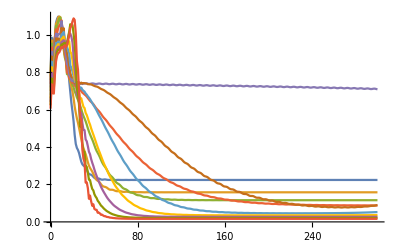

```mathematica
ListLinePlot[SnumU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_conf

```mathematica
PNAU08μTs//Dimensions
subRDMeigensU08μTs//Dimensions
```

{11,299,3}

{11,299,3}

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
subRDMeigensU08μTs[[1]][[1]][[1]][[1]]
```

1.

```mathematica
SconfNsU08μTs=-Map[Total,(PNAU08μTs*subRDMeigensU08μTs*Log[subRDMeigensU08μTs]),{3}];
```

```mathematica
SconfNsU08μTs//Dimensions
```

{11,299,3}

```mathematica
SconfN1U08μTs=SconfNsU08μTs[[All,All,1]];
SconfN2U08μTs=SconfNsU08μTs[[All,All,2]];
SconfN3U08μTs=SconfNsU08μTs[[All,All,3]];
```

```mathematica
SconfN1U08μTs//Dimensions
SconfN2U08μTs//Dimensions
SconfN3U08μTs//Dimensions
```

{11,299}

{11,299}

{11,299}

```mathematica
SconfU08μTs=Plus[SconfN1U08μTs,SconfN2U08μTs,SconfN3U08μTs];
%//Dimensions
```

{11,299}

```mathematica
Export[NotebookDirectory[]<>"SconfU08μTs_L89N2_mu21;;31_Sort_2_t1.mx",SconfU08μTs];
```

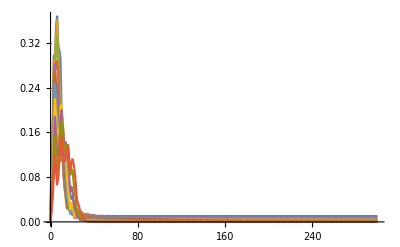

```mathematica
ListLinePlot[SconfU08μTs,DataRange->MinMax@{0,timenum},PlotRange->All]
```

#### S_tot

```mathematica
StotU08μTs=SnumU08μTs+SconfU08μTs;
%//Dimensions
```

{11,299}

```mathematica
Export[NotebookDirectory[]<>"StotU08μTs_L89N2_mu21;;31_Sort_2_t1.mx",StotU08μTs];
```

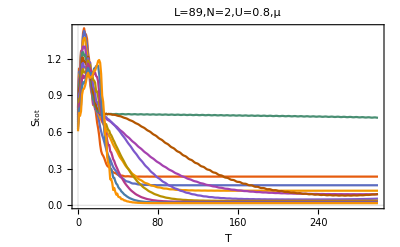

```mathematica
ListLinePlot[StotU08μTs,DataRange->MinMax@{0,timenum},PlotTheme->{"LargeLabels","SansLabels","Scientific"},FrameLabel->{"T","S_tot"},PlotLabel->"L=89,N=2,U=0.8,μ",PlotRange->All]
```

## dynamic S_E U=0.8(t-301-600) Δt=1.

### Basic

#### Import U=0.8,Ts

```mathematica
ψU08μTs=Import[NotebookDirectory[]<>"finalpsit_L89N2_U08_mus_t1.mx"];(*导入系统的本征态*)
```

Import::nffil: 在 Import 期间没有找到文件 /home/sun/Tim/Exact diagonalization/non-hermitian/Model B/newPotential_2/L89/EE/dynamic/U08/1-300_t1/finalpsit_L89N2_U08_mus_t1.mx.

```mathematica
ψU08μTs//Dimensions
```

{}

```mathematica
(*ψ2=Import[NotebookDirectory[]<>"ED_vec_L89N2Tmu1_U08(0.6_1.1)_g(0_1.1_0.05)_hang_B.mx"];(*导入系统的本征态*)*)
```

```mathematica
RDMACoordinates=Import[NotebookDirectory[]<>"RDMACoordinates_L89N2_Sort_2.mx"];
```

Import::nffil: 在 Import 期间没有找到文件 /home/sun/Tim/Exact diagonalization/non-hermitian/Model B/newPotential_2/L89/EE/dynamic/U08/1-300_t1/RDMACoordinates_L89N2_Sort_2.mx.

```mathematica
RDMACoordinates//Dimensions
```

{}

```mathematica
CordinateInDMAB=Import[NotebookDirectory[]<>"CordinateInDMAB_L89N2.mx"];
```

Import::nffil: 在 Import 期间没有找到文件 /home/sun/Tim/Exact diagonalization/non-hermitian/Model B/newPotential_2/L89/EE/dynamic/U08/1-300_t1/CordinateInDMAB_L89N2.mx.

```mathematica
CordinateInDMAB//Dimensions
```

{}

#### time --- Δt=1

```mathematica
Δt=1;
timenum=301;;600;
```

```mathematica
U08P=First[Position[Uvalues,0.8]][[1]]
```

17

```mathematica
Export[NotebookDirectory[]<>"start_mark.txt",timenum];
```

### COMPUTE μ 1-2

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=1;;2;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

Part::take: 无法在 $Failed 中提取位置 1 至 2.

{3}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

Part::partd: 部分指定 $Failed⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 $Failed⟦2⟧ 比对象深度更长.

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{}

{2}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

Part::pkspec1: 表达式 $Failed→1 不能作为部分指定使用.

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

Merge::list1: 参数 $Failed→$Failed⟦2⟧ 不是一个有效的 Associations 列表或者规则或者规则列表.

Merge::list1: 参数 $Failed→$Failed 不是一个有效的 Associations 列表或者规则或者规则列表.

Merge::list1: 参数 $Failed→1 不是一个有效的 Associations 列表或者规则或者规则列表.

General::stop: 在本次计算中，Merge::list1 的进一步输出将被抑制.

Part::pkspec1: 表达式 Merge[Total][$Failed→1] 不能作为部分指定使用.

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

Part::pkspec1: 表达式 Merge[Total][$Failed→1] 不能作为部分指定使用.

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

SparseArray::list: SparseArray[Merge[Total][$Failed→$Failed⟦2⟧]] 中位置 1 处应该是一个列表.

SparseArray::list: SparseArray[Merge[Total][$Failed→$Failed]] 中位置 1 处应该是一个列表.

SparseArray::list: SparseArray[Merge[Total][$Failed→1]] 中位置 1 处应该是一个列表.

General::stop: 在本次计算中，SparseArray::list 的进一步输出将被抑制.

Part::pkspec1: 表达式 SparseArray[Merge[Total][$Failed→1]] 不能作为部分指定使用.

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

Part::take: 无法在 time 中提取位置 301 至 600.

### COMPUTE μ 3-4

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=3;;4;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 5-6

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=5;;6;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 7-8

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=7;;8;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 9-10

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=9;;10;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 11-12

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=11;;12;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 13-14

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=13;;14;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 15-16

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=15;;16;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 17-18

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=17;;18;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 19-20

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=19;;20;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 21-22

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=21;;22;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 23-24

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=23;;24;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 25-26

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=25;;26;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 27-28

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=27;;28;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ 29-30

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=29;;30;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{2,303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{2,303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{2,303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
(*sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;*)
```

```mathematica
sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{2,303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs,{2}];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre,{2}];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs,{2}];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{2,303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```

### COMPUTE μ31

#### μposition

===========================================

μposition 的取值范围为Range[μnum]-----μnum=31

===========================================

```mathematica
μposition=31;
```

```mathematica
ψU08μTs=ψU08μTs[[μposition,timenum]];
%//Dimensions
```

{303,4005}

#### Elements

```mathematica
RDMnonzeroElementsU08μTsPre=ψU08μTs[[All,#]]&/@Thread[CordinateInDMAB];
```

```mathematica
RDMnonzeroElementsU08μTsPre//Dimensions
```

{2,303,1068255}

```mathematica
RDMnonzeroElementsU08μTs=RDMnonzeroElementsU08μTsPre[[1]]*Conjugate[RDMnonzeroElementsU08μTsPre[[2]]];
```

```mathematica
RDMnonzeroElementsU08μTs//Dimensions
```

{303,1068255}

如果从头开始，那么timeP的起始值为2

```mathematica
RDMACoordinates//Dimensions
RDMnonzeroElementsU08μTs//Dimensions
```

{1068255,2}

{303,1068255}

```mathematica
(*sparseElementsPreU08μTs=Map[Thread[Rule[RDMACoordinates, #]] &, RDMnonzeroElementsU08μTs, {2}];*)
```

```mathematica
(*sparseElementsPreU04μTs=Table[Thread[RDMACoordinates->RDMnonzeroElementsU08μTs[[μp]][[timeP]]],{μp,5},{timeP,2,timenum}];*)
```

```mathematica
sparseElementsPreU08μTs=MapThread[Rule,{RDMACoordinates,#}]&/@RDMnonzeroElementsU08μTs;
```

```mathematica
sparseElementsPreU08μTs//Dimensions
```

{303,1068255}

```mathematica
(*%//Dimensions*)
```

#### computation sparse for only one μ

```mathematica
merge=Merge[Total];
```

```mathematica
sparseElementsU08μTspre=Map[merge,sparseElementsPreU08μTs];
```

```mathematica
(*sparseElementsU04μTspre=Map[merge,sparseElementsPreU08μTs,{2}];*)
```

```mathematica
(*sparseElementsU08μTspre//Dimensions*)
```

```mathematica
sparseElementsU08μTs=Map[Normal,sparseElementsU08μTspre];
```

```mathematica
(*sparseElementsU08μTs//Dimensions*)
```

```mathematica
(*sparseElementsU04μTs=Map[Normal,sparseElementsU08μTspre,{2}];*)
```

#### sparese matrix and export

```mathematica
RDMAmatrixU08μTs=Map[SparseArray,sparseElementsU08μTs];
```

```mathematica
RDMAmatrixU08μTs//Dimensions
```

{303,1035,1035}

```mathematica
(*RDMAmatrixU04μTs=Map[SparseArray,sparseElementsU08μTs,{2}];*)
```

```mathematica
Export[NotebookDirectory[]<>StringJoin["RDMAmatrix_U08_mu",ToString[MinMax@μvalues[[μposition]]],"_Ts_L89N2_t",ToString[MinMax@time[[timenum]]],"_t1.mx"],RDMAmatrixU08μTs];
```